## Section 4 Questions

#### Short Question 4.1 At this temperature, the uncertainty in the velocity of the electron exceeds the magnitude of the velocity itself, so the velocity of the electron cannot be known with any certainty. The same could be said for its momentum. Thus, by the Heisenberg Uncertainty Principle, the position of the electron should be very well-defined, to the extent that it could be said to be in a position eigenstate. Hence, the scattering of the electron will not be obscured by its wavepacket, so quantum mechanics is appropriate for this scenario. For the hydrogen molecule and the argon atom, the uncertainty in their velocity is around 1/10th of the magnitude of their respective velocities. There is thus still significant uncertainty associated with their velocity values, but not enough to allow for their positions to be well defined in accordance with the Uncertainty Principle. Thus a classical description for these systems is appropriate.

### Short Question 4.2 The angular distributions will be given by the scattered amplitude f(θ), the form of which is given in Equations (4.56) and (4.57) of Section 4 of the notes.

```mathematica
f=Al+ⅈ Bl;
Al=1/(2k)(2l+1)Sin[2 (n+1/2)Pi]LegendreP[l,Cos[θ]];
Bl=1/(2k)(2l+1)(1-Cos[2 (n+1/2)Pi])LegendreP[l,Cos[θ]];
```

s-wave scattering angular distribution (magnitude squared thereof) for n = 0, for -π ≤ θ ≤ π. These conditions are used in the below plots. Is this the right thing to be plotting (“sketching”)?

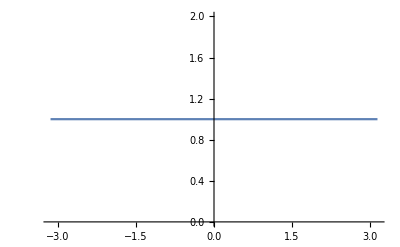

```mathematica
Plot[Abs[f/.{k->1,l->0,n->1}]^2,{θ,-Pi,Pi}]
```

p-wave scattering angular distribution (magnitude squared thereof).

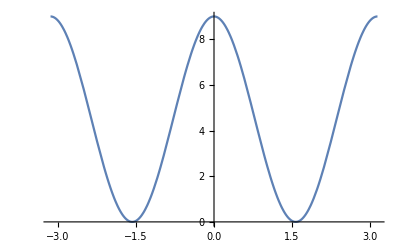

```mathematica
Plot[Abs[f/.{k->1,l->1,n->1}]^2,{θ,-Pi,Pi}]
```

d-wave scattering angular distribution (magnitude squared thereof).

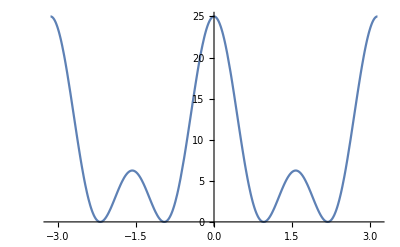

```mathematica
Plot[Abs[f/.{k->1,l->2,n->3}]^2,{θ,-Pi,Pi}]
```

### Short Question 4.3 (a) When kD = nπ/2 for odd integers n, then the cross section becomes infinitely large according to Equation (4.69). However, in this low energy limit, the interaction energy E was defined such that λ/(2π) >> D ⇒ 1 >> (2 π)/λ D = kD (and kD is strictly positive so 0 < kD << 1). Thus this scenario is not possible, so we do not have to worry about the cross section diverging in this low energy limit. (b) From Equation (4.69), sinδ_0≈ kD ((tan (k_i D))/(k_i D) - 1) so when tan kD = kD, sinδ_0 ≈ 0 ⇒ δ_0= 0, nπ for integer n. We thus get phase shifts of integer multiples of π. What does this mean and why does this matter?

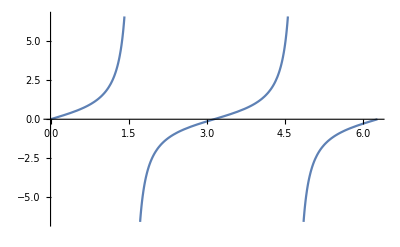

```mathematica
Plot[Tan[x],{x,0,2Pi}]
```

### Short Question 4.4 Ar (Z=18) → σ_T=1 Å^2 and K (Z=19) → σ_T=350 Å^2 1 eV electrons will undergo low collisions with the atomic targets above. As stated in the notes, most of the low energy scattering is driven by polarisation effects, so the dipole polarisability (how much each atom responds to the electric field of an incident electron) will be a key factor here. The dipole polarisability of K (α = 293) is more than 20 times that of Ar (α = 11.08), so potassium is much more susceptible to being polarised by the incident electron. As Ar has a closed outer shell of electrons (an energetically favourable and stable state), it is thus a symmetric atom and so it makes sense that any external electric field that is applied to this atom (by an incoming electron, say) would not have much of an effect, since the atomic electrons of argon will not move much in response to this introduced electric field. In contrast, the lone outer shell of potassium is much more susceptible to the external electric field that will be introduced by any inbound electrons, which will make scattering of the incident electron and the potassium atom away from each other much more probable when they approach each other. Some thoughts for He and He* (metastable excited state): He has a closed shell of electrons so low polarisability so low susceptibility to any external electric field and thus the influence of the incoming electron on this atom will be negligible. Therefore low scattering probability so low cross section. For He*, one of the electrons now lies in an outer shell by itself, so the atom may is no longer spherically symmetric and thus is much more polarisable. Thus the incident electron will have a much more significant effect on the atom since it will see the lone outer electron and be repelled (i.e. scatter off it). In short, it all has to do with the outer electronic structure of the atoms and whether or not they are spherically symmetric. If they aren’t, they will more readily be polarised, inducing an electric field in them that will interact with the electric field of the incident electron at much greater distances than if the atom cannot be readily polarised because it has a closed outer shell. This will increase the effective area of the atom as seen by the electron, as electrostatic repulsion is a much more long-ranged interaction than hard sphere collisions, and the electric field of a polarised atom will be stronger at greater distances from the atom than that of a single outer electron. As a result, the cross section of a polarised atom will exceed that of one which is unpolarised, which is why the cross sections for He* and K are much greater than those for He and Ar.